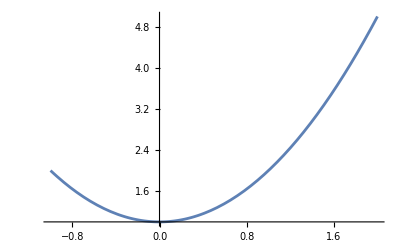

```mathematica
f[x_]:=1+x^2;
range={-1,2,0.1};

Plot[f[x],{x, range[[1]], range[[2]]}]
```

```mathematica
approximatingPoints[xii_,w_,n_:10]:=Join[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]

LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]

approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
errorFunc[xii_, w_]:=With[{af=approxFunc[xii,w]},Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}]]
```

```mathematica
Manipulate[Plot[approxFunc[xii, w][x], {x, -1, 10}], {xii, 0, 1}, {w, 0, 1}]
```

```mathematica
plots={};
gridDescentPlotMinimize[loss_, varsAndBounds_, iters_:20, tempInput_:None, d_:0.0001]:=
Module[
{temp=If[tempInput===None, Mean[varsAndBounds[[All, 4]]]/10,tempInput],
indices=Flatten[Table@@Prepend[varsAndBounds, varsAndBounds[[All, 1]]], Length[varsAndBounds]-1],
gradients, progress=PrintTemporary["0% Complete"],
plotFunc=Switch[Length[varsAndBounds],
1,ListPlot[#, PlotRange->varsAndBounds[[1, 2;;3]]]&,
2,ListPlot[#, PlotRange->varsAndBounds[[All, 2;;3]]]&,
3,ListPointPlot3D[#, PlotRange->varsAndBounds[[All, 2;;3]]]&,
_,"No Plot"&]},
indices=Table[Clip[#[[i]], varsAndBounds[[i, 2;;3]]- d],{i, Length[varsAndBounds]}]&/@indices;
plots={plotFunc[indices]};
Table[
gradients=ParallelMap[(loss@@@(#+d*IdentityMatrix[Length[varsAndBounds]])-loss@@#)/d&,indices];
gradients=Table[Clip[#[[i]],varsAndBounds[[i,2;;3]]],{i,Length[varsAndBounds]}]&/@gradients;
indices=indices-temp*gradients;
indices=Table[Clip[#[[i]],varsAndBounds[[i,2;;3]]],{i,Length[varsAndBounds]}]&/@indices;
AppendTo[plots,plotFunc[indices]];
NotebookDelete[progress];
progress=PrintTemporary[ToString[Round[100*iter/iters]]<>"% Minimized"];,{iter,iters}];
indices[[First[PositionSmallest[ParallelMap[loss@@#&,indices]]]]]
]
```

```mathematica
gridDescentPlotMinimize[errorFunc, {{xii, 0, 1, 0.1}, {w, 0, 1, 0.1}},3,0.01]
ListAnimate[plots]
```

{0.37,0.9699}